```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
ru[r_]:=Piecewise[{{1,0≤r<0.4},{4/3,0.4<=r≤48.90},{1,r>48.90}}];
```

```mathematica
LogLogPlot[ru[r],{r,0,201.5}]
```

```mathematica
Itbdata=ReadList["Itbdata.txt",{Number,Number}];
```

```mathematica
a1[b_]:=b*NIntegrate[((1+ru[r])*ru[r])/r^3/.r->√(b^2+z^2),{z,0,∞}]
LogLinearPlot[a1[b],{b,0.0001,201.5},PlotRange->All]
```

```mathematica
rItb=Interpolation[Itbdata];
```

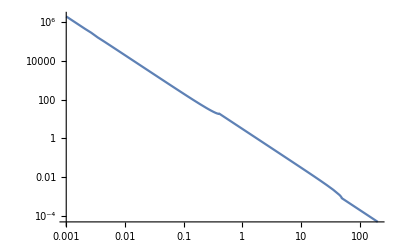

```mathematica
rrItb[b_]:=Piecewise[{{2/b^2,b<-201.5},{rItb[-b],-201.5≤b≤-0.001},{2/b^2,-0.001<b<0.001},{rItb[b],0.001<=b≤201.5},{2/b^2,b>201.5}}];
LogLogPlot[rrItb[b],{b,0.001,201.5},PlotRange->All]
```

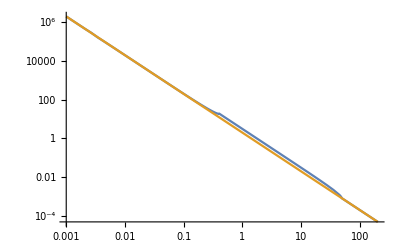

```mathematica
LogLogPlot[{rrItb[b],2/b^2},{b,0.001,201.5},PlotRange->All]
```

```mathematica
zl=0.3;
zs=1;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^15;(*Msun*)
sigmav=300;(*km s^-1*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]
DA2[zl,zs]/(DA[zl]*DA[zs])

DAc[zl]
DAc[zs]
DA2c[zl,zs]
DA2c[zl,zs]/(DAc[zl]*DAc[zs])
```

919.403

1653.06

1055.45

0.000694452

946.444

1701.68

1086.49

0.00067461

```mathematica
thetaE=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs]
thetaEc=(4Pi*sigmav^2)/c^2*DA2c[zl,zs]/DAc[zs]
thetaE*DA[zl]
```

8.02339×10^-6

8.02339×10^-6

0.00737673

```mathematica
rhoSISGR[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/r^2;
```

```mathematica
SigmaSISGR[ksi_]:=sigmav^2/(2*G)*30.85678*10^18*1/ksi;
```

```mathematica
alphaSISGR[ksi_]:=(4Pi*sigmav^2)/c^2*DA2[zl,zs]/DA[zs];
```

```mathematica
alphaSISGR[ksi]
```

8.02339×10^-6

```mathematica
rhoSISMG[r_]:=sigmav^2/(2*Pi*G)*30.85678*10^18*1/(ru[r]*r^2);
```

```mathematica
SigmaSISMG[ksi_]:=2NIntegrate[rhoSISMG[r]/.r->(ksi^2+z^2)^(1/2),{z,0,Infinity}];
```

```mathematica
SigmaSISMGana[ksi_]:=Piecewise[{{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*(ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]-3/4*ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0<=ksi<0.4},{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*(3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0.4≤ksi≤48.9},{sigmav^2/(Pi*G)*30.85678*10^18*1/ksi*Pi/2,ksi>48.9}}];
```

```mathematica
ksiSigmaSISMGana[ksi_]:=Piecewise[{{sigmav^2/(Pi*G)*30.85678*10^18*(ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]-3/4*ArcTan[((0.4^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0<=ksi<0.4},{sigmav^2/(Pi*G)*30.85678*10^18*(3/4 ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]+Pi/2-ArcTan[((48.9^2-ksi^2)^(1/2))/ksi]),0.4≤ksi≤48.9},{sigmav^2/(Pi*G)*30.85678*10^18*Pi/2,ksi>48.9}}];
```

```mathematica
alphaSISMG[ksi_]:=DA2[zl,zs]/DA[zs]*(2*G)/c^2*1/(30.85678*10^18)*NIntegrate[ksiSigmaSISMGana[ksip]*(ksi-ksip*Cos[phi])*Itbdata[(ksi^2+ksip^2-2ksi*ksip*Cos[phi])^(1/2)],{phi,0,2Pi},{ksip,0,1000}];
```

```mathematica
test1[ksi_]:=DA2[zl,zs]/DA[zs]*(2*G)/c^2*1/(30.85678*10^18)*NIntegrate[ksiSigmaSISMGana[ksip]*(ksi-ksip*Cos[phi])*Itbdata[(ksi^2+ksip^2-2ksi*ksip*Cos[phi])^(1/2)],{phi,0,2Pi},{ksip,0,1000}];
```